## Skateboard Results

```mathematica
nbDir=NotebookDirectory[];

sk50ISRWOErr = Import[FileNameJoin[{nbDir,"results", "aws_6_all", "results_all", "skateboard_1372_50_spanning_2_Vspanning_2_v2_D5_X0.0_05_Apr_19_24_57", "charts.json" }], "RawJSON"];

sk50HC = Import[FileNameJoin[{nbDir,"results", "aws_18_sk_other_err", "results", "skateboard_1372_50_spanning_2_sb_Vspanning_2_D5_Cw_M1_13_Apr_00_05_04", "charts.json" }], "RawJSON"];
sk50ISR = Import[FileNameJoin[{nbDir,"results", "aws_16_sk_test_err", "results", "skateboard_1372_50_spanning_2_sb_Vspanning_2_v2_D5_Cw_M1_12_Apr_23_24_18", "charts.json" }], "RawJSON"];
sk50RSF = Import[FileNameJoin[{nbDir,"results", "aws_18_sk_other_err", "results", "skateboard_1372_50_spanning_2_sb_Vspanning_2_v3_D5_Cw_M1_13_Apr_00_06_46", "charts.json" }], "RawJSON"];

skSwarMer=Import[FileNameJoin[{nbDir,"results", "swarmer-20node-comp-5", "results", "skateboard_1372_50_spanning_2", "10-Apr-17_32_43", "charts.json" }], "RawJSON"];


sk5ISR  = Import[FileNameJoin[{nbDir,"results", "aws_17_sk_test_err", "results", "skateboard_1372_5_spanning_2_sb_Vspanning_2_v2_D5_Cw_M1_12_Apr_23_38_23", "charts.json" }], "RawJSON"];
sk10ISR  = Import[FileNameJoin[{nbDir,"results", "aws_17_sk_test_err", "results", "skateboard_1372_10_spanning_2_sb_Vspanning_2_v2_D5_Cw_M1_12_Apr_23_40_04", "charts.json" }], "RawJSON"];
sk150ISR  = Import[FileNameJoin[{nbDir,"results", "aws_17_sk_test_err", "results", "skateboard_1372_150_spanning_2_sb_Vspanning_2_v2_D5_Cw_M1_12_Apr_23_41_46", "charts.json" }], "RawJSON"];
sk200ISR  = Import[FileNameJoin[{nbDir,"results", "aws_16_sk_test_err", "results", "skateboard_1372_200_spanning_2_sb_Vspanning_2_v2_D5_Cw_M1_12_Apr_23_26_00", "charts.json" }], "RawJSON"];


s=10; (* Conver cm to mm *)
sk50HCt = sk50HC[["t"]];
sk50ISRt = sk50ISR[["t"]];
sk50ISRWOErrt = sk50ISRWOErr[["t"]];
sk50RSFt = sk50RSF[["t"]];
skSwarMert = skSwarMer["t"];
skSwarMercd = skSwarMer["cd"]*s;
skSwarMerhd = skSwarMer["hd"]*s;
sk50HCcd = sk50HC[["cd"]]*s;
sk50ISRcd = sk50ISR[["cd"]]*s;
sk50ISRWOErrcd = sk50ISRWOErr[["cd"]]*s;
sk50RSFcd = sk50RSF[["cd"]]*s;
sk50HChd = sk50HC[["hd"]]*s;
sk50ISRhd = sk50ISR[["hd"]]*s;
sk50ISRWOErrhd = sk50ISRWOErr[["hd"]]*s;
sk50RSFhd = sk50RSF[["hd"]]*s;
sk5ISRt = sk5ISR[["t"]];
sk10ISRt = sk10ISR[["t"]];
sk150ISRt = sk150ISR[["t"]];
sk200ISRt = sk200ISR[["t"]];
sk5ISRhd = sk5ISR[["hd"]]*s;
sk10ISRhd = sk10ISR[["hd"]]*s;
sk150ISRhd = sk150ISR[["hd"]]*s;
sk200ISRhd = sk200ISR[["hd"]]*s;
sk5ISRcd = sk5ISR[["cd"]]*s;
sk10ISRcd = sk10ISR[["cd"]]*s;
sk150ISRcd = sk150ISR[["cd"]]*s;
sk200ISRcd = sk200ISR[["cd"]]*s;
```

### Figure 15

```mathematica
skSwarMerCompHD = ListLinePlot[
{
Transpose[{skSwarMert,skSwarMerhd}],
Transpose[{sk50ISRWOErrt,sk50ISRWOErrhd}]
},
PlotRange->{0.1, 1000},
PlotRangePadding->None,
PlotMarkers->None,
ScalingFunctions->"Log10",
Ticks->{Automatic, {0.1, 1, 10, 100, 1000}},
AxesLabel->{Column[{"Time","(Second)"}, Alignment->Center],HoldForm[HD "(mm)"]},
PlotLabels->{
Callout["SwarMer",{Scaled[0.5],Above}],
Callout["Swarical (ISR)",{Scaled[0.2],Below}]
},
PlotLabel->None,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
PlotStyle->96,
AspectRatio->1/2.5
]
```

-Graphics-

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardSwarMerISRComparison_HD.jpg"}],skSwarMerCompHD,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardSwarMerISRComparison_HD.jpg

```mathematica
skSwarMerCompCD = ListLinePlot[
{
Transpose[{skSwarMert,skSwarMercd}],
Transpose[{sk50ISRWOErrt,sk50ISRWOErrcd}]
},
PlotRange->{0.1, 1000},
PlotRangePadding->None,
PlotMarkers->None,
ScalingFunctions->"Log10",
Ticks->{Automatic, {0.1, 1, 10, 100, 1000}},
AxesLabel->{Column[{"Time","(Second)"}, Alignment->Center],HoldForm[CD "(mm)"]},
PlotLabels->{
Callout["SwarMer",{Scaled[0.5],Above}],
Callout["Swarical (ISR)",{Scaled[0.15],Above}]
},
PlotLabel->None,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
PlotStyle->96
]
```

-Graphics-

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardSwarMerISRComparison_CD.jpg"}],skSwarMerCompCD,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardSwarMerISRComparison_CD.jpg

### Figure 13.a

```mathematica
skVarCompHD = ListLinePlot[
{
Transpose[{sk50HCt,sk50HChd}],
Transpose[{sk50ISRt,sk50ISRhd}],
Transpose[{sk50RSFt,sk50RSFhd}]
},
PlotRange->{10, 1000},
PlotRangePadding->None,
PlotMarkers->None,
ScalingFunctions->"Log10",
Ticks->{Automatic, {0.1, 1, 10, 100, 1000}},
AxesLabel->{Column[{"Time","(Second)"}, Alignment->Center],HoldForm[HD "(mm)"]},
PlotLabels->{
Callout["HC",{Scaled[0.25],Above}],
Callout["ISR",{Scaled[0.15],Above}],
Callout["RSF",{Scaled[0.5],Below}]
},
PlotLabel->None,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
PlotStyle->96,
AspectRatio->1/3
]
```

-Graphics-

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardVariantComparison_HD_G50_werr.jpg"}],skVarCompHD,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardVariantComparison_HD_G50_werr.jpg

### Figure 13.b

```mathematica
skVarCompCD = ListLinePlot[
{
Transpose[{sk50HCt,sk50HCcd}],
Transpose[{sk50ISRt,sk50ISRcd}],
Transpose[{sk50RSFt,sk50RSFcd}]
},
PlotRange->{10, 1000},
PlotRangePadding->None,
PlotMarkers->None,
ScalingFunctions->"Log10",
Ticks->{Automatic, {0.1, 1, 10, 100, 1000}},
AxesLabel->{Column[{"Time","(Second)"}, Alignment->Center],HoldForm[CD "(mm)"]},
PlotLabels->{
Callout["HC",{Scaled[0.25], Above}],
Callout["ISR",{Scaled[0.1],Below}],
Callout["RSF",{Scaled[0.5],Above}]
},
PlotLabel->None,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
PlotStyle->96,
AspectRatio->1/3
]
```

-Graphics-

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardVariantComparison_CD_G50_werr.jpg"}],skVarCompCD,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardVariantComparison_CD_G50_werr.jpg

### Figure 14.a

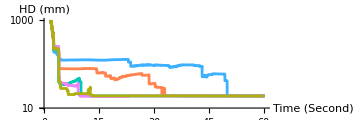

```mathematica
skISRGCompHD = ListLinePlot[
{
Transpose[{sk5ISRt,sk5ISRhd}],
Transpose[{sk10ISRt,sk10ISRhd}],
Transpose[{sk50ISRt,sk50ISRhd}],
Transpose[{sk150ISRt,sk150ISRhd}],
Transpose[{sk200ISRt,sk200ISRhd}]
},
PlotRange->{10, 1000},
PlotRangePadding->None,
PlotMarkers->None,
ScalingFunctions->"Log10",
Ticks->{Automatic, {0.1, 1, 10, 100, 1000}},
AxesLabel->{Column[{"Time","(Second)"}, Alignment->Center],HoldForm[HD "(mm)"]},
(*PlotLabels->{
Callout["G=5",{Scaled[0.9],Above}],
Callout["G=10",{Scaled[0.8],Above}],
Callout["G=50",{Scaled[0.28],Above}],
Callout["G=150",{Scaled[0.25],Above}], 
Callout["G=200",{Scaled[0.48],Above}]
},*)
PlotLegends->Placed[{"G=5", "G=10", "G=50", "G=150", "G=200"}, Below],
PlotLabel->None,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
PlotStyle->96,
AspectRatio->1/3
]
```

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardGroupSizeComparison_HD_ISR_werr.jpg"}],skISRGCompHD,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardGroupSizeComparison_HD_ISR_werr.jpg

### Figure 14.b

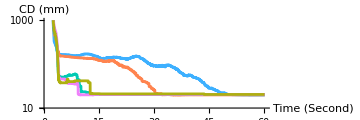

```mathematica
skISRGCompCD= ListLinePlot[
{
Transpose[{sk5ISRt,sk5ISRcd}],
Transpose[{sk10ISRt,sk10ISRcd}],
Transpose[{sk50ISRt,sk50ISRcd}],
Transpose[{sk150ISRt,sk150ISRcd}],
Transpose[{sk200ISRt,sk200ISRcd}]
},
PlotRange->{10, 1000},
PlotRangePadding->None,
PlotMarkers->None,
ScalingFunctions->"Log10",
Ticks->{Automatic, {0.1, 1, 10, 100, 1000}},
AxesLabel->{Column[{"Time","(Second)"}, Alignment->Center],"CD (mm)"},
(*PlotLabels->{
Callout["G=5",{Scaled[0.9],Above}],
Callout["G=10",{Scaled[0.6],Above}],
Callout["G=50",{10, 100}],
Callout["G=150",{Scaled[0.07],Below}], 
Callout["G=200",{Scaled[0.32],Above}]
},*)
PlotLegends->Placed[{"G=5", "G=10", "G=50", "G=150", "G=200"}, Below],
PlotLabel->None,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
PlotStyle->96,
AspectRatio->1/3
]
```

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardGroupSizeComparison_CD_ISR_werr.jpg"}],skISRGCompCD,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardGroupSizeComparison_CD_ISR_werr.jpg

## Swarm-tree and FLS-tree Stats

```mathematica
nbDir=NotebookDirectory[];

sk5stats = Import[FileNameJoin[{nbDir,"assets", "skateboard_1372_5_spanning_2_sb_stats.json"}], "RawJSON"];
sk10stats = Import[FileNameJoin[{nbDir,"assets", "skateboard_1372_10_spanning_2_sb_stats.json"}], "RawJSON"];
sk50stats = Import[FileNameJoin[{nbDir,"assets", "skateboard_1372_50_spanning_2_sb_stats.json"}], "RawJSON"];
sk150stats = Import[FileNameJoin[{nbDir,"assets", "skateboard_1372_150_spanning_2_sb_stats.json"}], "RawJSON"];
sk200stats = Import[FileNameJoin[{nbDir,"assets", "skateboard_1372_200_spanning_2_sb_stats.json"}], "RawJSON"];

s=1;
sk5GroupSize = sk5stats["group_size"];
sk5DistGroup = sk5stats["dist_in_groups"]*s;
sk5DistAcrossGroup = sk5stats["dist_across_groups"]*s;
sk5BFGroup = sk5stats["bf_in_groups"];
sk5BFAcrossGroup = sk5stats["bf_across_groups"];
sk10GroupSize = sk10stats["group_size"];
sk10DistGroup = sk10stats["dist_in_groups"]*s;
sk10DistAcrossGroup = sk10stats["dist_across_groups"]*s;
sk10BFGroup = sk10stats["bf_in_groups"];
sk10BFAcrossGroup = sk10stats["bf_across_groups"];
sk50GroupSize = sk50stats["group_size"];
sk50DistGroup = sk50stats["dist_in_groups"]*s;
sk50DistAcrossGroup = sk50stats["dist_across_groups"]*s;
sk50BFGroup = sk50stats["bf_in_groups"];
sk50BFAcrossGroup = sk50stats["bf_across_groups"];
sk150GroupSize = sk150stats["group_size"];
sk150DistGroup = sk150stats["dist_in_groups"]*s;
sk150DistAcrossGroup = sk150stats["dist_across_groups"]*s;
sk150BFGroup = sk150stats["bf_in_groups"];
sk150BFAcrossGroup = sk150stats["bf_across_groups"];
sk200GroupSize = sk200stats["group_size"];
sk200DistGroup = sk200stats["dist_in_groups"]*s;
sk200DistAcrossGroup = sk200stats["dist_across_groups"]*s;
sk200BFGroup = sk200stats["bf_in_groups"];
sk200BFAcrossGroup = sk200stats["bf_across_groups"];
```

### Figure 11

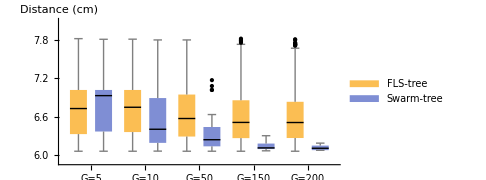

```mathematica
skDistBox=BoxWhiskerChart[
<|
"G=5"-><|"FLS-tree"->sk5DistGroup, "Swarm-tree"->sk5DistAcrossGroup|>,
"G=10"-><|"FLS-tree"->sk10DistGroup, "Swarm-tree"->sk10DistAcrossGroup|>,
"G=50"-><|"FLS-tree"->sk50DistGroup, "Swarm-tree"->sk50DistAcrossGroup|>,
"G=150"-><|"FLS-tree"->sk150DistGroup, "Swarm-tree"->sk150DistAcrossGroup|>,
"G=200"-><|"FLS-tree"->sk200DistGroup, "Swarm-tree"->sk200DistAcrossGroup|>
|>,
{{"MedianMarker", Black}, {"Outliers", Automatic, Black}, {"FarOutliers", Automatic, Gray}},
AxesLabel->{None,"Distance (cm)"},
AxesOrigin->{0, 5.9},
PlotRange->{Automatic, {5.9,8.09}},
(*Ticks->{Automatic, {5,7,9,11}},*)
ChartLegends->{Placed[{"FLS-tree", "Swarm-tree"}, {0.89, .999}]},
ChartLegends->Automatic,
ChartLabels->{Automatic, None},
Frame->False,
Axes->True,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
AspectRatio->1/2
]
```

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardDistanceBox_2.jpg"}],skDistBox,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardDistanceBox_2.jpg

### Figure 12

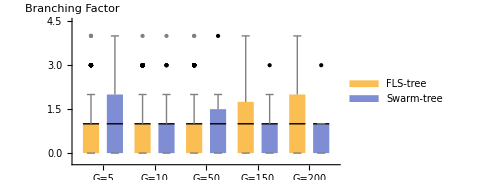

```mathematica
skBranchBox=BoxWhiskerChart[
<|
"G=5"-><|"FLS-tree"->sk5BFGroup, "Swarm-tree"->sk5BFAcrossGroup|>,
"G=10"-><|"FLS-tree"->sk10BFGroup, "Swarm-tree"->sk10BFAcrossGroup|>,
"G=50"-><|"FLS-tree"->sk50BFGroup, "Swarm-tree"->sk50BFAcrossGroup|>,
"G=150"-><|"FLS-tree"->sk150BFGroup, "Swarm-tree"->sk150BFAcrossGroup|>,
"G=200"-><|"FLS-tree"->sk200BFGroup, "Swarm-tree"->sk200BFAcrossGroup|>
|>,
{{"MedianMarker", Black}, {"Outliers", Automatic, Black}, {"FarOutliers", Automatic, Gray}},
AxesLabel->{None,"Branching Factor"},
ChartLegends->{Placed[{"FLS-tree", "Swarm-tree"}, {0.89, .999}]},
ChartLegends->Automatic,
PlotRange->{Automatic, {-.3,4.5}},
AxesOrigin->{0, -.3},
ChartLabels->{Automatic, None},
Frame->False,
Axes->True,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
AspectRatio->1/2
]
```

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardBranchingFactorBox_2.jpg"}],skBranchBox,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardBranchingFactorBox_2.jpg

### Figure 10

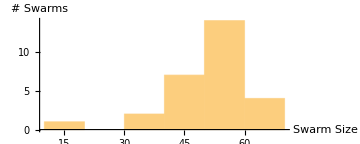

```mathematica
skSwarmSize = Histogram[
sk50GroupSize,
PlotRange->Automatic,
PlotRangePadding->Automatic,
AxesLabel->{Column[{"Swarm Size"}, Alignment->Center],"# Swarms"},
PlotLabel->None,
LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},
ImageSize->Medium,
AspectRatio->1/2.5
]
```

```mathematica
Export[FileNameJoin[{nbDir,"figures", "SkateboardSwarmSize_G50_2.jpg"}],skSwarmSize,"JPEG", ImageResolution->300]
```

/Users/hamed/Documents/Holodeck/Swarical/figures/SkateboardSwarmSize_G50_2.jpg